```mathematica
Sqrt[36]
```

6

```mathematica
Sqrt[45]
```

3 √5

```mathematica
Sqrt[50]
```

5 √2

```mathematica
Sin[180/3]
```

Sin[60]

```mathematica
Sin[Pi/3]
```

```mathematica
(√3)/2
```

```mathematica
Cos[2Pi/3]
```

-1/2

```mathematica
Tan[4Pi/5]
```

-√(5-2 √5)

```mathematica
A={4,5,6,9,12}
B={2,3,4,8,9}
Union[A,B]
```

{4,5,6,9,12}

{2,3,4,8,9}

{2,3,4,5,6,8,9,12}

```mathematica
Intersection[A,B]
```

{4,9}

```mathematica
Subsets[A]
```

{{},{4},{5},{6},{9},{12},{4,5},{4,6},{4,9},{4,12},{5,6},{5,9},{5,12},{6,9},{6,12},{9,12},{4,5,6},{4,5,9},{4,5,12},{4,6,9},{4,6,12},{4,9,12},{5,6,9},{5,6,12},{5,9,12},{6,9,12},{4,5,6,9},{4,5,6,12},{4,5,9,12},{4,6,9,12},{5,6,9,12},{4,5,6,9,12}}

```mathematica
Length[A]
```

5

```mathematica
Solve[x^2-5x+6==0]
```

{{x→2},{x→3}}

```mathematica
Solve[5x^2-2x+3==0]
```

{{x→1/5 (1-ⅈ √14)},{x→1/5 (1+ⅈ √14)}}

```mathematica
f[x_]={3x^2-4}
g[x_] = {3x - 1}
g[f[x]]
```

{-4+3 x^2}

{-1+3 x}

{{-1+3 (-4+3 x^2)}}

```mathematica
f[g[x]]
```

{{-4+3 (-1+3 x)^2}}

```mathematica
f[x_]={3x^2-4}
g[x_]={3x-1}
g[g[x]]
```

{-4+3 x^2}

{-1+3 x}

{{-1+3 (-1+3 x)}}

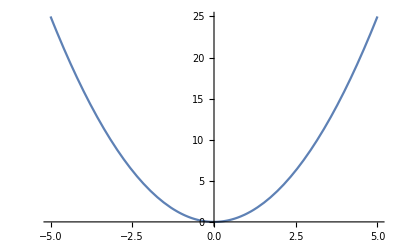

```mathematica
Plot[x^2,{x,-5,5}]
```

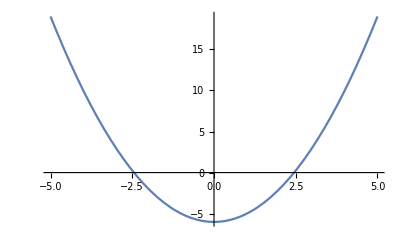

```mathematica
Plot[x^2-6,{x,-5,5}]
```

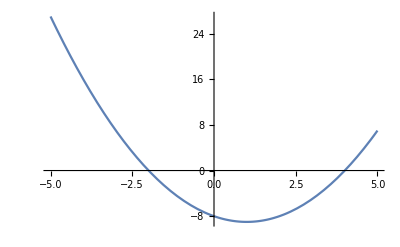

```mathematica
Plot[x^2-2x-8,{x,-5,5}]
```

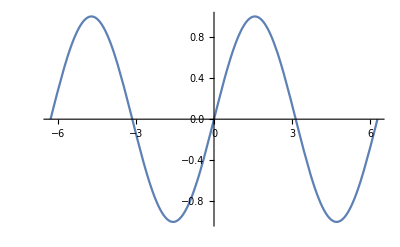

```mathematica
Plot[Sin[x],{x,-2Pi,2Pi}]
```

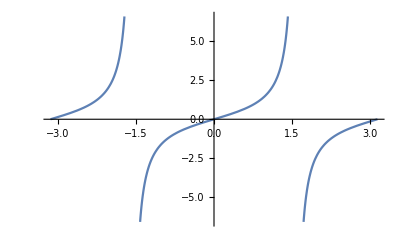

```mathematica
Plot[Tan[x],{x,-Pi,Pi}]
```

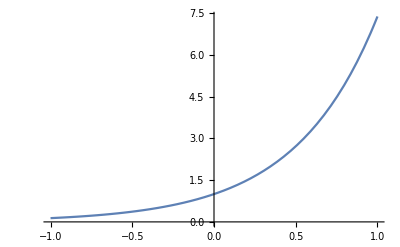

```mathematica
Plot[Exp[2x],{x,-1,1}]
```

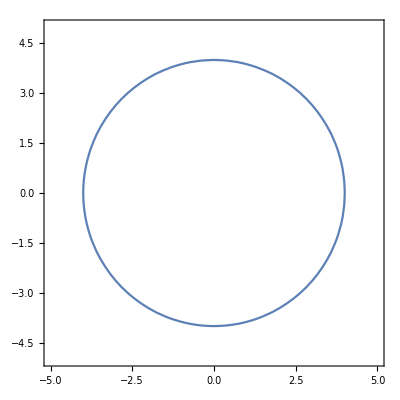

```mathematica
ContourPlot[x^2+y^2==16,{x,-5,5},{y,-5,5}]
```

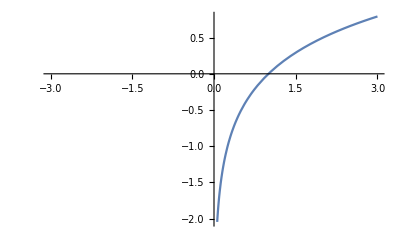

```mathematica
Plot[Log[4,x],{x,-3,3}]
```

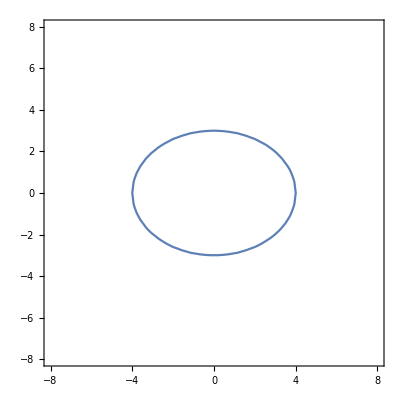

```mathematica
ContourPlot[x^2/16+y^2/9==1,{x,-8,8},{y,-8,8}]
```

```mathematica
Show[%6,Axes->True,AxesStyle->Black]
```

-Graphics-

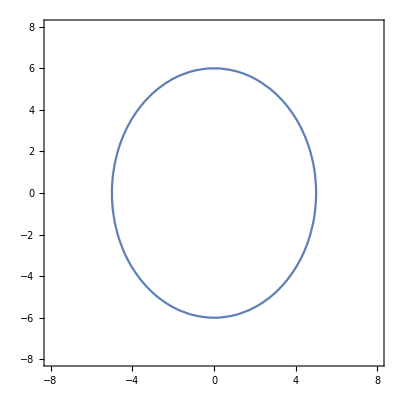

```mathematica
ContourPlot[x^2/25+y^2/36==1,{x,-8,8},{y,-8,8}]
```

```mathematica
Show[%8,Axes->True,AxesStyle->Black]
```

-Graphics-

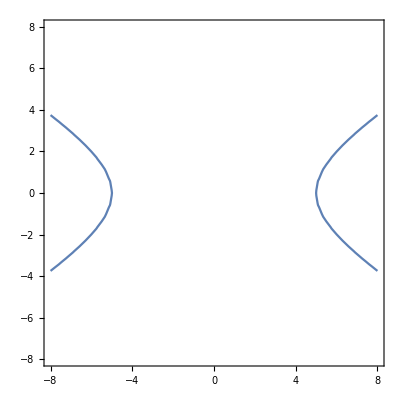

```mathematica
ContourPlot[x^2/25-y^2/9==1,{x,-8,8},{y,-8,8}]
```

```mathematica
A={{2,5,7},{0,4,-9},{3,-2,6}}
MatrixForm[A]
B={{3,-1,2},{8,0,5},{-4,7,1}}
MAtrixForm[B]
A+B
```

{{2,5,7},{0,4,-9},{3,-2,6}}

(2 | 5 | 7
0 | 4 | -9
3 | -2 | 6)

{{3,-1,2},{8,0,5},{-4,7,1}}

MAtrixForm[{{3,-1,2},{8,0,5},{-4,7,1}}]

{{5,4,9},{8,4,-4},{-1,5,7}}

```mathematica
MatrixForm[A+B]
```

(5 | 4 | 9
8 | 4 | -4
-1 | 5 | 7)

```mathematica
MatrixForm[A B]
```

(6 | -5 | 14
0 | 0 | -45
-12 | -14 | 6)

```mathematica
MatrixForm[B A]
```

(6 | -5 | 14
0 | 0 | -45
-12 | -14 | 6)

```mathematica
MatrixForm[Inverse[B]]
```

(-1 | 3/7 | -1/7
-4/5 | 11/35 | 1/35
8/5 | -17/35 | 8/35)

```mathematica
Det[A]
```

-207

```mathematica
MatrixRank[A]
```

3

```mathematica
MatrixForm[Transpose[A]]
```

(2 | 0 | 3
5 | 4 | -2
7 | -9 | 6)

```mathematica
Det[A]
```

-207

```mathematica
Total[{1,8,27,64,125,216,343}]
```

784

```mathematica
Total[{1,3,6,10,15,21,28}]
```

84

```mathematica
Sum[n,{n,1,10}]
```

55

```mathematica
Sum[n^2,{n,1,10}]
```

385

```mathematica
Sum[n^3,{n,1,10}]
```

3025

```mathematica
FindSequenceFunction[{2,4,6,8},n]
```

2 n

```mathematica
FindSequenceFunction[{1 3,3 5, 5 7, 7 9},n]
```

-1+4 n^2

```mathematica
FindSequenceFunction[{1,8,27,64},n]
```

```mathematica
FindSequenceFunction[{1,8,27,64,125},n]
```

n^3

```mathematica
a={2,3,4}
b={-3,6,8}
a+b
```

{2,3,4}

{-3,6,8}

{-1,9,12}

```mathematica
Norm[a]
```

Norm[a]

```mathematica
a={2,3,4}
b={-3,6,8}
Norm[a]
```

{2,3,4}

{-3,6,8}

√29

```mathematica
Dot[a,b]
```

44

```mathematica
Cross[a,b]
```

{0,-28,21}

```mathematica
Normalize[a]
```

{2/(√29),3/(√29),4/(√29)}

```mathematica
VectorAngle[a,b]
```

ArcCos[44/(√3161)]

```mathematica
FindSequenceFunction[{1,8,27,64},n]
```

FindSequenceFunction[{1,8,27,64},n]

```mathematica
FindSequenceFunction[{1,2,3,4,5},n]
```

n